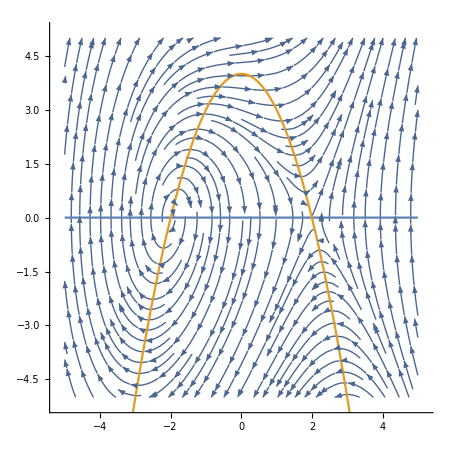

5.5

{-1,-1}

{0.5+1.93649 ⅈ,0.5-1.93649 ⅈ}

```mathematica
f1[x1_, x2_]:=x2;
f2[x1_, x2_]:=x1^2+x2-4;
Show[StreamPlot[{Sign[f1[x1, x2]],f2[x1, x2]/f1[x1, x2] Sign[f1[x1, x2]]},{x1,-5,5},{x2,-5,5},StreamPoints->Fine,VectorScale->0.01,Frame->False,Axes->True], Plot[{Solve[f1[x1, x2]==0, x2][[1,1,2]], Solve[f2[x1, x2]==0, x2][[1,1,2]]}, {x1, -5, 5}]]
With[{x1=2.5, x2=0.5},f2[x1, x2]/f1[x1, x2]]
With[{x1=1, x2=-1},{Sign[f1[x1, x2]], Sign[f2[x1, x2]]}]
Eigenvalues[{{D[f1[x1, x2], x1], D[f1[x1, x2], x2]},{D[f2[x1, x2], x1], D[f2[x1, x2], x2]}}/.x1->-2]//N
```

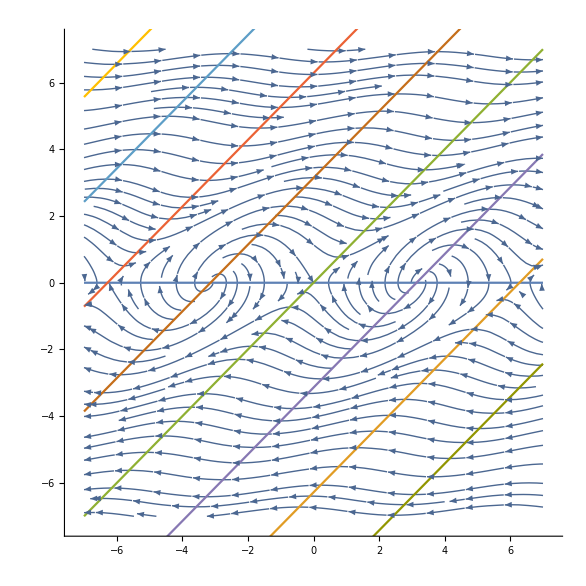

{-1,1}

{{x2→ConditionalExpression[x1-2 π C[1],C[1]∈Integers]},{x2→ConditionalExpression[-π+x1-2 π C[1],C[1]∈Integers]}}

{0.5+0.866025 ⅈ,0.5-0.866025 ⅈ}

```mathematica
f1[x1_, x2_]:=x2;
f2[x1_, x2_]:=Sin[x1-x2];
Show[StreamPlot[{Sign[f1[x1, x2]],f2[x1, x2]/f1[x1, x2] Sign[f1[x1, x2]]},{x1,-7,7},{x2,-7,7},StreamPoints->Fine,Frame->False,Axes->True], Plot[{0,x1-2 π,x1,x1+2 π,-π+x1,-π+x1+2 π,-π+x1+4 π,x1+4 π,,x1-4 π+π}, {x1, -7,7}]]
With[{x1=-6, x2=-1},{Sign[f1[x1, x2]], Sign[f2[x1, x2]]}]
Solve[f2[x1, x2]==0, x2]
A[x1_, x2_]:={{D[f1[x1, x2], x1], D[f1[x1, x2], x2]},{D[f2[x1, x2], x1], D[f2[x1, x2], x2]}}//Evaluate
Eigenvalues[A[Pi, 0]]//N
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

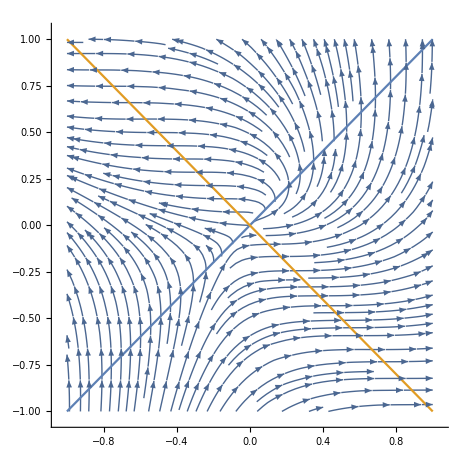

-9

{-1,1}

{{1,-1},{2 (x1+x2),2 (x1+x2)}}

```mathematica
f1[x1_, x2_]:=x1-x2;
f2[x1_, x2_]:=(x1+x2)^2;
Show[StreamPlot[{Sign[f1[x1, x2]],f2[x1, x2]/f1[x1, x2] Sign[f1[x1, x2]]},{x1,-1,1},{x2,-1,1},StreamPoints->Fine,Frame->False,Axes->True], Plot[{Solve[f1[x1, x2]==0, x2][[1,1,2]], Solve[f2[x1, x2]==0, x2][[1,1,2]]}, {x1, -1,1}]]
With[{x1=-2, x2=-1},f2[x1, x2]/f1[x1, x2]]
With[{x1=-2, x2=-1},{Sign[f1[x1, x2]], Sign[f2[x1, x2]]}]
A[x1_, x2_]:={{D[f1[x1, x2], x1], D[f1[x1, x2], x2]},{D[f2[x1, x2], x1], D[f2[x1, x2], x2]}}//Evaluate
A[x1, x2]
```

```mathematica
Solve[Sin[x1-x2]==0, x2]
```

{{x2→ConditionalExpression[x1-2 π C[1],C[1]∈Integers]},{x2→ConditionalExpression[-π+x1-2 π C[1],C[1]∈Integers]}}